```mathematica
rootpath="~/Dropbox/jobb/research/0000Active/marker/Code/";
If[!MemberQ[$Path,rootpath],
AppendTo[$Path,rootpath];
];
fl=rootpath<>"Data/IsingMajoranaChainOnlyDerived.hdf5";
```

```mathematica
p=Function[{x,y},"/SystemSizes/"<>ToString[x]<>"/PeriodicBC/deltaValues/"<>ToString[y]];
```

```mathematica
NbrOfdeltaValues17=89;
deltas17=Import[fl,p[1,#]<>"/delta"]&/@Range[NbrOfdeltaValues17];
```

```mathematica
allmarkers17=Function[deltaval,With[{NbrOfIterations=Import[fl,p[1,deltaval]<>"/NbrOfIterations"]},
Import[fl,p[1,deltaval]<>"/Iterations/"<>ToString[#]<>"/MeanChiralMarker"]&/@Range[NbrOfIterations]
]]/@Range[NbrOfdeltaValues17];
allmarkers17=allmarkers17[[Ordering[deltas17]]];
deltas17=deltas17[[Ordering[deltas17]]];
```

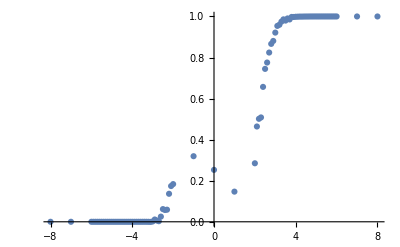

```mathematica
ListPlot[MapThread[{#1,#2}&,{deltas17,Median/@allmarkers17}]]
```

```mathematica
p2=Position[deltas17,2.][[1,1]];
```

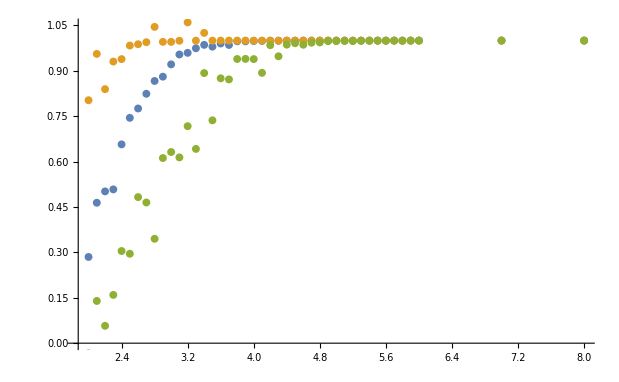

```mathematica
ListPlot[{
MapThread[{#1,#2}&,{deltas17[[p2;;]],(Median/@allmarkers17)[[p2;;]]}]
,
MapThread[{#1,#2}&,{deltas17[[p2;;]],(Quantile[#,0.97]&/@allmarkers17)[[p2;;]]}]
,
MapThread[{#1,#2}&,{deltas17[[p2;;]],(Quantile[#,0.09]&/@allmarkers17)[[p2;;]]}]
},
PlotRange->{0,1.05}]
```

```mathematica
Length/@(allmarkers17[[p2;;]])
```

{116,58,64,52,58,56,68,65,50,56,114,54,62,70,70,56,64,59,52,60,125,61,72,57,61,54,65,58,63,65,114,57,59,64,50,66,71,56,51,57,130,62,58}

```mathematica
Import[fl,"/SystemSizes/4/l"]
```

14

```mathematica
NbrOfdeltaValues14=Import[fl,"/SystemSizes/4/PeriodicBC/NbrOfdeltaValues"];
deltas14=Import[fl,p[4,#]<>"/delta"]&/@Range[NbrOfdeltaValues14];
allmarkers14=Function[deltaval,With[{NbrOfIterations=Import[fl,p[4,deltaval]<>"/NbrOfIterations"]},
Import[fl,p[4,deltaval]<>"/Iterations/"<>ToString[#]<>"/MeanChiralMarker"]&/@Range[NbrOfIterations]
]]/@Range[NbrOfdeltaValues14];
allmarkers14=allmarkers14[[Ordering[deltas14]]];
deltas14=deltas14[[Ordering[deltas14]]];
```